```mathematica
IntPlus[J_,Jone_,Jtwo_,p_,z_Real] := NIntegrate[1/(8Pi)p*(Cos[k]-1)/(J^2-2J*Jtwo-z^2+2J(Jone*Cos[k]+2Jtwo*Cos[k]^2)),{k,-Pi,Pi}]
```

```mathematica
NullsHolm[Jtwo_,z_] := 1+ 2*IntPlus[1,0.3,Jtwo,0.3,z]
```

```mathematica
FindRoot[NullsHolm[-0.00,z],{z,0.5916079783099615}]
```

{z→0.591608}

```mathematica
Clear[IntPlus,NullsHolm,G,P]
```

```mathematica
(√(-4 J^3 q+8J*q^2-2 J^3 l+4 J^2q*l+J^2 l^2))/(√(-4J*q-2J*l))/.{J->1,q->0.3,l->0.3}
```

0.591608+0. ⅈ

```mathematica
Inv[Jone_,Jtwo_] := Piecewise[{{ArcCos[-Jone/(4*Jtwo)],Jone<4*Jtwo},{Pi,Jone>4*Jtwo}}]
```

```mathematica
Lister[Plusminus_,Xstart_,StartIteration_] := Module[{lst={{Xstart,FindRoot[NullsHolm[Xstart,z],{z,StartIteration}]}}},
Do[
Jtwoo=Plusminus(n+1)*0.0005;
p= Check[FindRoot[NullsHolm[Jtwoo,z]==0,{z,z/.lst[[n,2]]}
],z->0];
AppendTo[lst,{Jtwoo,p}];
,{n,1,199,1}
];
lst
]
```

```mathematica
moduler[list_] := Module[{lst := {}},
Do [
AppendTo [lst,{list[[n,1]],z/.list[[n,2]]}];
,{n,1,200,1}
];
lst
]
```

```mathematica
Fueger[lst1_,lst2_] := Module[{lst={}},
Do[
AppendTo[lst,lst1[[n]]]
,{n,1,200,1}];
Do[
AppendTo[lst,lst2[[n]]]
,{n,1,200,1}];
lst
]
```

```mathematica
moduler[Lister[1,0.005,0.5916079783099615]]
```

{{0.005,0.598404},{0.01,0.605018},{0.015,0.611447},{0.02,0.617686},{0.025,0.623732},{0.03,0.629578},{0.035,0.635218},{0.04,0.640644},{0.045,0.645849},{0.05,0.650822},{0.055,0.655556},{0.06,0.660038},{0.065,0.664258},{0.07,0.668205},{0.075,0.671867},{0.08,0.675233},{0.085,0.67829},{0.09,0.68103},{0.095,0.683443},{0.1,0.685519}}

```mathematica
moduler[Lister[-1,-0.005,0.5916079783099615]]
```

{{-0.005,0.584632},{-0.01,0.577477},{-0.015,0.570145},{-0.02,0.562635},{-0.025,0.554946},{-0.03,0.547076},{-0.035,0.539024},{-0.04,0.530785},{-0.045,0.522356},{-0.05,0.513732},{-0.055,0.504907},{-0.06,0.495873},{-0.065,0.486624},{-0.07,0.477149},{-0.075,0.467437},{-0.08,0.457478},{-0.085,0.447257},{-0.09,0.436758},{-0.095,0.425963},{-0.1,0.414851}}

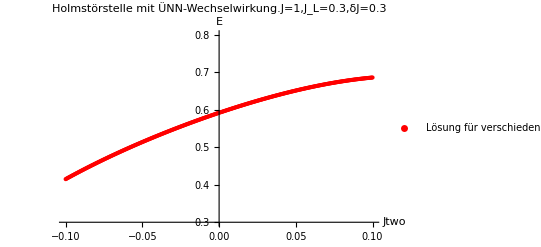

```mathematica
P = ListPlot[Fueger[moduler[Lister[1,0.0005,0.5916079783099615]],moduler[Lister[-1,-0.0005,0.5916079783099615]]],AxesLabel->{Jtwo,"E"},PlotLegends->{"Lösung für verschiedene Jtwos"},PlotLabel->"Holmstörstelle mit ÜNN-Wechselwirkung.J=1,J_L=0.3,δJ=0.3",PlotRange->{0.3,0.8},PlotStyle->Red]
```

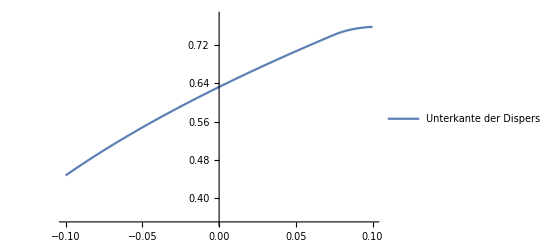

```mathematica
G = Plot[Sqrt[1+2*(0.3*Cos[Inv[0.3,Jtwo]]+Jtwo*Cos[2*Inv[0.3,Jtwo]])],{Jtwo,-0.1,0.1},PlotRange->{0.35,0.78},PlotLegends->{"Unterkante der Dispersion"}]
```

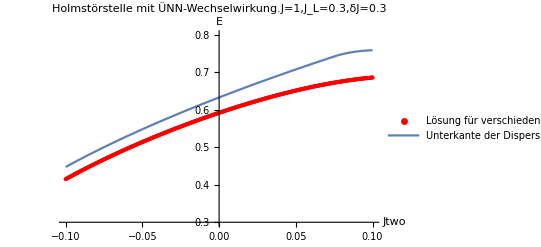

```mathematica
Show[P,G]
```

```mathematica
GLow[J_,Jone_,Jtwo_] := Sqrt[J+2*(Jone*Cos[Inv[Jone,Jtwo]]+Jtwo*Cos[2*Inv[Jone,Jtwo]])]
```

```mathematica
differ[PlusMinus_,Jone_,list_] := Module[{lst = {}},
Do[
Jtwoo = PlusMinus*n*0.0005;
AppendTo[lst,{Jtwoo,GLow[1,Jone,Jtwoo]-list[[n,2]]}];
,{n,1,200,1}
];
lst
]
```

```mathematica
differ[-1,0.3,moduler[Lister[-1,-0.005,0.5916079783099615]]]
```

{{-0.005,0.0398679},{-0.01,0.0389641},{-0.015,0.0381313},{-0.02,0.0373653},{-0.025,0.0366623},{-0.03,0.036019},{-0.035,0.0354325},{-0.04,0.0349002},{-0.045,0.03442},{-0.05,0.0339903},{-0.055,0.0336095},{-0.06,0.0332768},{-0.065,0.0329915},{-0.07,0.0327534},{-0.075,0.0325626},{-0.08,0.0324199},{-0.085,0.0323265},{-0.09,0.032284},{-0.095,0.032295},{-0.1,0.0323625}}

```mathematica
differ[1,0.3,moduler[Lister[1,0.005,0.5916079783099615]]]
```

{{0.005,0.0419083},{0.01,0.043056},{0.015,0.044297},{0.02,0.0456386},{0.025,0.0470885},{0.03,0.0486552},{0.035,0.0503479},{0.04,0.0521764},{0.045,0.0541514},{0.05,0.0562844},{0.055,0.0585871},{0.06,0.0610723},{0.065,0.0637528},{0.07,0.0666418},{0.075,0.651009},{0.08,0.0722633},{0.085,0.0735699},{0.09,0.073953},{0.095,0.0736291},{0.1,0.0727681}}

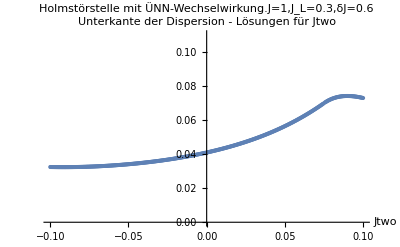

```mathematica
ListPlot[Fueger[differ[-1,0.3,moduler[Lister[-1,-0.0005,0.5916079783099615]]],differ[1,0.3,moduler[Lister[1,0.0005,0.5916079783099615]]]],AxesLabel->{Jtwo,"Unterkante der Dispersion - Lösungen für Jtwo"}, PlotLabel->"Holmstörstelle mit ÜNN-Wechselwirkung.J=1,J_L=0.3,δJ=0.6"]
```

```mathematica
Fueger[moduler[Lister[1,0.0005,0.5916079783099615]],moduler[Lister[-1,-0.0005,0.5916079783099615]]]
```

{{0.0005,0.592296},{0.001,0.592982},{0.0015,0.593666},{0.002,0.594348},{0.0025,0.595029},{0.003,0.595707},{0.0035,0.596384},{0.004,0.597059},{0.0045,0.597733},{0.005,0.598404},{0.0055,0.599074},{0.006,0.599742},{0.0065,0.600408},{0.007,0.601072},{0.0075,0.601734},{0.008,0.602395},{0.0085,0.603053},{0.009,0.60371},{0.0095,0.604365},{0.01,0.605018},{0.0105,0.605669},{0.011,0.606319},{0.0115,0.606966},{0.012,0.607612},{0.0125,0.608256},{0.013,0.608898},{0.0135,0.609538},{0.014,0.610176},{0.0145,0.610812},{0.015,0.611447},{0.0155,0.612079},{0.016,0.61271},{0.0165,0.613339},{0.017,0.613966},{0.0175,0.61459},{0.018,0.615214},{0.0185,0.615835},{0.019,0.616454},{0.0195,0.617071},{0.02,0.617686},{0.0205,0.6183},{0.021,0.618911},{0.0215,0.619521},{0.022,0.620128},{0.0225,0.620734},{0.023,0.621337},{0.0235,0.621939},{0.024,0.622539},{0.0245,0.623136},{0.025,0.623732},{0.0255,0.624326},{0.026,0.624917},{0.0265,0.625507},{0.027,0.626095},{0.0275,0.62668},{0.028,0.627264},{0.0285,0.627845},{0.029,0.628425},{0.0295,0.629002},{0.03,0.629578},{0.0305,0.630151},{0.031,0.630722},{0.0315,0.631292},{0.032,0.631859},{0.0325,0.632424},{0.033,0.632987},{0.0335,0.633548},{0.034,0.634106},{0.0345,0.634663},{0.035,0.635218},{0.0355,0.63577},{0.036,0.63632},{0.0365,0.636868},{0.037,0.637414},{0.0375,0.637958},{0.038,0.6385},{0.0385,0.639039},{0.039,0.639576},{0.0395,0.640111},{0.04,0.640644},{0.0405,0.641175},{0.041,0.641703},{0.0415,0.642229},{0.042,0.642753},{0.0425,0.643275},{0.043,0.643794},{0.0435,0.644311},{0.044,0.644826},{0.0445,0.645338},{0.045,0.645849},{0.0455,0.646356},{0.046,0.646862},{0.0465,0.647365},{0.047,0.647866},{0.0475,0.648365},{0.048,0.648861},{0.0485,0.649355},{0.049,0.649847},{0.0495,0.650336},{0.05,0.650822},{0.0505,0.651307},{0.051,0.651789},{0.0515,0.652268},{0.052,0.652745},{0.0525,0.65322},{0.053,0.653692},{0.0535,0.654162},{0.054,0.654629},{0.0545,0.655093},{0.055,0.655556},{0.0555,0.656015},{0.056,0.656473},{0.0565,0.656927},{0.057,0.657379},{0.0575,0.657829},{0.058,0.658276},{0.0585,0.65872},{0.059,0.659162},{0.0595,0.659601},{0.06,0.660038},{0.0605,0.660472},{0.061,0.660903},{0.0615,0.661332},{0.062,0.661758},{0.0625,0.662182},{0.063,0.662602},{0.0635,0.66302},{0.064,0.663436},{0.0645,0.663848},{0.065,0.664258},{0.0655,0.664665},{0.066,0.66507},{0.0665,0.665472},{0.067,0.66587},{0.0675,0.666267},{0.068,0.66666},{0.0685,0.66705},{0.069,0.667438},{0.0695,0.667823},{0.07,0.668205},{0.0705,0.668584},{0.071,0.668961},{0.0715,0.669334},{0.072,0.669705},{0.0725,0.670072},{0.073,0.670437},{0.0735,0.670799},{0.074,0.671158},{0.0745,0.671514},{0.075,0.671867},{0.0755,0.672217},{0.076,0.672564},{0.0765,0.672908},{0.077,0.673249},{0.0775,0.673588},{0.078,0.673923},{0.0785,0.674255},{0.079,0.674584},{0.0795,0.67491},{0.08,0.675233},{0.0805,0.675552},{0.081,0.675869},{0.0815,0.676183},{0.082,0.676493},{0.0825,0.676801},{0.083,0.677105},{0.0835,0.677406},{0.084,0.677704},{0.0845,0.677999},{0.085,0.67829},{0.0855,0.678579},{0.086,0.678864},{0.0865,0.679146},{0.087,0.679425},{0.0875,0.679701},{0.088,0.679973},{0.0885,0.680242},{0.089,0.680508},{0.0895,0.680771},{0.09,0.68103},{0.0905,0.681287},{0.091,0.681539},{0.0915,0.681789},{0.092,0.682035},{0.0925,0.682278},{0.093,0.682518},{0.0935,0.682754},{0.094,0.682987},{0.0945,0.683217},{0.095,0.683443},{0.0955,0.683666},{0.096,0.683885},{0.0965,0.684101},{0.097,0.684314},{0.0975,0.684524},{0.098,0.68473},{0.0985,0.684932},{0.099,0.685131},{0.0995,0.685327},{0.1,0.685519},{-0.0005,0.590918},{-0.001,0.590227},{-0.0015,0.589534},{-0.002,0.588839},{-0.0025,0.588142},{-0.003,0.587444},{-0.0035,0.586744},{-0.004,0.586041},{-0.0045,0.585338},{-0.005,0.584632},{-0.0055,0.583924},{-0.006,0.583215},{-0.0065,0.582504},{-0.007,0.581791},{-0.0075,0.581077},{-0.008,0.58036},{-0.0085,0.579642},{-0.009,0.578922},{-0.0095,0.578201},{-0.01,0.577477},{-0.0105,0.576752},{-0.011,0.576025},{-0.0115,0.575296},{-0.012,0.574566},{-0.0125,0.573833},{-0.013,0.573099},{-0.0135,0.572363},{-0.014,0.571626},{-0.0145,0.570886},{-0.015,0.570145},{-0.0155,0.569402},{-0.016,0.568657},{-0.0165,0.567911},{-0.017,0.567162},{-0.0175,0.566412},{-0.018,0.56566},{-0.0185,0.564907},{-0.019,0.564151},{-0.0195,0.563394},{-0.02,0.562635},{-0.0205,0.561874},{-0.021,0.561111},{-0.0215,0.560347},{-0.022,0.559581},{-0.0225,0.558813},{-0.023,0.558043},{-0.0235,0.557271},{-0.024,0.556498},{-0.0245,0.555723},{-0.025,0.554946},{-0.0255,0.554167},{-0.026,0.553386},{-0.0265,0.552604},{-0.027,0.55182},{-0.0275,0.551034},{-0.028,0.550246},{-0.0285,0.549456},{-0.029,0.548665},{-0.0295,0.547871},{-0.03,0.547076},{-0.0305,0.546279},{-0.031,0.54548},{-0.0315,0.54468},{-0.032,0.543877},{-0.0325,0.543073},{-0.033,0.542267},{-0.0335,0.541459},{-0.034,0.540649},{-0.0345,0.539837},{-0.035,0.539024},{-0.0355,0.538208},{-0.036,0.537391},{-0.0365,0.536572},{-0.037,0.535751},{-0.0375,0.534928},{-0.038,0.534103},{-0.0385,0.533277},{-0.039,0.532448},{-0.0395,0.531618},{-0.04,0.530785},{-0.0405,0.529951},{-0.041,0.529115},{-0.0415,0.528277},{-0.042,0.527437},{-0.0425,0.526595},{-0.043,0.525751},{-0.0435,0.524905},{-0.044,0.524058},{-0.0445,0.523208},{-0.045,0.522356},{-0.0455,0.521503},{-0.046,0.520647},{-0.0465,0.51979},{-0.047,0.518931},{-0.0475,0.518069},{-0.048,0.517206},{-0.0485,0.51634},{-0.049,0.515473},{-0.0495,0.514604},{-0.05,0.513732},{-0.0505,0.512859},{-0.051,0.511984},{-0.0515,0.511106},{-0.052,0.510227},{-0.0525,0.509345},{-0.053,0.508462},{-0.0535,0.507576},{-0.054,0.506688},{-0.0545,0.505799},{-0.055,0.504907},{-0.0555,0.504013},{-0.056,0.503117},{-0.0565,0.502219},{-0.057,0.501319},{-0.0575,0.500417},{-0.058,0.499512},{-0.0585,0.498606},{-0.059,0.497697},{-0.0595,0.496786},{-0.06,0.495873},{-0.0605,0.494958},{-0.061,0.494041},{-0.0615,0.493122},{-0.062,0.4922},{-0.0625,0.491276},{-0.063,0.49035},{-0.0635,0.489422},{-0.064,0.488491},{-0.0645,0.487559},{-0.065,0.486624},{-0.0655,0.485687},{-0.066,0.484747},{-0.0665,0.483805},{-0.067,0.482861},{-0.0675,0.481915},{-0.068,0.480966},{-0.0685,0.480015},{-0.069,0.479062},{-0.0695,0.478107},{-0.07,0.477149},{-0.0705,0.476188},{-0.071,0.475226},{-0.0715,0.474261},{-0.072,0.473293},{-0.0725,0.472323},{-0.073,0.471351},{-0.0735,0.470376},{-0.074,0.469399},{-0.0745,0.468419},{-0.075,0.467437},{-0.0755,0.466453},{-0.076,0.465466},{-0.0765,0.464476},{-0.077,0.463484},{-0.0775,0.46249},{-0.078,0.461492},{-0.0785,0.460493},{-0.079,0.45949},{-0.0795,0.458485},{-0.08,0.457478},{-0.0805,0.456468},{-0.081,0.455455},{-0.0815,0.45444},{-0.082,0.453422},{-0.0825,0.452401},{-0.083,0.451378},{-0.0835,0.450351},{-0.084,0.449323},{-0.0845,0.448291},{-0.085,0.447257},{-0.0855,0.44622},{-0.086,0.44518},{-0.0865,0.444137},{-0.087,0.443091},{-0.0875,0.442043},{-0.088,0.440992},{-0.0885,0.439937},{-0.089,0.43888},{-0.0895,0.43782},{-0.09,0.436758},{-0.0905,0.435692},{-0.091,0.434623},{-0.0915,0.433551},{-0.092,0.432476},{-0.0925,0.431398},{-0.093,0.430317},{-0.0935,0.429233},{-0.094,0.428146},{-0.0945,0.427056},{-0.095,0.425963},{-0.0955,0.424866},{-0.096,0.423766},{-0.0965,0.422663},{-0.097,0.421557},{-0.0975,0.420448},{-0.098,0.419335},{-0.0985,0.418219},{-0.099,0.4171},{-0.0995,0.415977},{-0.1,0.414851}}

```mathematica
Fueger[differ[-1,0.3,moduler[Lister[-1,-0.0005,0.5916079783099615]]],differ[1,0.3,moduler[Lister[1,0.0005,0.5916079783099615]]]]
```

{{-0.0005,0.040746},{-0.001,0.0406453},{-0.0015,0.0405454},{-0.002,0.0404463},{-0.0025,0.0403479},{-0.003,0.0402504},{-0.0035,0.0401536},{-0.004,0.0400576},{-0.0045,0.0399624},{-0.005,0.0398679},{-0.0055,0.0397742},{-0.006,0.0396812},{-0.0065,0.039589},{-0.007,0.0394976},{-0.0075,0.0394068},{-0.008,0.0393168},{-0.0085,0.0392276},{-0.009,0.039139},{-0.0095,0.0390512},{-0.01,0.0389641},{-0.0105,0.0388777},{-0.011,0.038792},{-0.0115,0.038707},{-0.012,0.0386227},{-0.0125,0.0385391},{-0.013,0.0384562},{-0.0135,0.0383739},{-0.014,0.0382924},{-0.0145,0.0382115},{-0.015,0.0381313},{-0.0155,0.0380517},{-0.016,0.0379729},{-0.0165,0.0378947},{-0.017,0.0378171},{-0.0175,0.0377402},{-0.018,0.0376639},{-0.0185,0.0375883},{-0.019,0.0375133},{-0.0195,0.037439},{-0.02,0.0373653},{-0.0205,0.0372922},{-0.021,0.0372198},{-0.0215,0.0371479},{-0.022,0.0370767},{-0.0225,0.0370061},{-0.023,0.0369362},{-0.0235,0.0368668},{-0.024,0.036798},{-0.0245,0.0367299},{-0.025,0.0366623},{-0.0255,0.0365953},{-0.026,0.036529},{-0.0265,0.0364632},{-0.027,0.036398},{-0.0275,0.0363334},{-0.028,0.0362694},{-0.0285,0.0362059},{-0.029,0.036143},{-0.0295,0.0360807},{-0.03,0.036019},{-0.0305,0.0359578},{-0.031,0.0358972},{-0.0315,0.0358372},{-0.032,0.0357777},{-0.0325,0.0357188},{-0.033,0.0356604},{-0.0335,0.0356026},{-0.034,0.0355453},{-0.0345,0.0354886},{-0.035,0.0354325},{-0.0355,0.0353768},{-0.036,0.0353217},{-0.0365,0.0352672},{-0.037,0.0352132},{-0.0375,0.0351597},{-0.038,0.0351067},{-0.0385,0.0350543},{-0.039,0.0350024},{-0.0395,0.034951},{-0.04,0.0349002},{-0.0405,0.0348498},{-0.041,0.0348},{-0.0415,0.0347507},{-0.042,0.034702},{-0.0425,0.0346537},{-0.043,0.0346059},{-0.0435,0.0345587},{-0.044,0.034512},{-0.0445,0.0344657},{-0.045,0.03442},{-0.0455,0.0343748},{-0.046,0.0343301},{-0.0465,0.0342859},{-0.047,0.0342422},{-0.0475,0.0341989},{-0.048,0.0341562},{-0.0485,0.034114},{-0.049,0.0340723},{-0.0495,0.034031},{-0.05,0.0339903},{-0.0505,0.03395},{-0.051,0.0339102},{-0.0515,0.033871},{-0.052,0.0338322},{-0.0525,0.0337938},{-0.053,0.033756},{-0.0535,0.0337187},{-0.054,0.0336818},{-0.0545,0.0336454},{-0.055,0.0336095},{-0.0555,0.0335741},{-0.056,0.0335392},{-0.0565,0.0335047},{-0.057,0.0334707},{-0.0575,0.0334372},{-0.058,0.0334042},{-0.0585,0.0333716},{-0.059,0.0333395},{-0.0595,0.0333079},{-0.06,0.0332768},{-0.0605,0.0332461},{-0.061,0.033216},{-0.0615,0.0331863},{-0.062,0.033157},{-0.0625,0.0331282},{-0.063,0.0331},{-0.0635,0.0330721},{-0.064,0.0330448},{-0.0645,0.0330179},{-0.065,0.0329915},{-0.0655,0.0329656},{-0.066,0.0329401},{-0.0665,0.0329151},{-0.067,0.0328906},{-0.0675,0.0328665},{-0.068,0.0328429},{-0.0685,0.0328198},{-0.069,0.0327972},{-0.0695,0.0327751},{-0.07,0.0327534},{-0.0705,0.0327321},{-0.071,0.0327114},{-0.0715,0.0326911},{-0.072,0.0326714},{-0.0725,0.032652},{-0.073,0.0326332},{-0.0735,0.0326148},{-0.074,0.032597},{-0.0745,0.0325796},{-0.075,0.0325626},{-0.0755,0.0325462},{-0.076,0.0325302},{-0.0765,0.0325147},{-0.077,0.0324997},{-0.0775,0.0324852},{-0.078,0.0324712},{-0.0785,0.0324576},{-0.079,0.0324446},{-0.0795,0.032432},{-0.08,0.0324199},{-0.0805,0.0324084},{-0.081,0.0323973},{-0.0815,0.0323867},{-0.082,0.0323766},{-0.0825,0.032367},{-0.083,0.0323579},{-0.0835,0.0323493},{-0.084,0.0323412},{-0.0845,0.0323336},{-0.085,0.0323265},{-0.0855,0.0323199},{-0.086,0.0323138},{-0.0865,0.0323083},{-0.087,0.0323033},{-0.0875,0.0322987},{-0.088,0.0322947},{-0.0885,0.0322913},{-0.089,0.0322883},{-0.0895,0.0322859},{-0.09,0.032284},{-0.0905,0.0322827},{-0.091,0.0322818},{-0.0915,0.0322816},{-0.092,0.0322818},{-0.0925,0.0322826},{-0.093,0.032284},{-0.0935,0.0322859},{-0.094,0.0322884},{-0.0945,0.0322914},{-0.095,0.032295},{-0.0955,0.0322991},{-0.096,0.0323038},{-0.0965,0.0323091},{-0.097,0.032315},{-0.0975,0.0323214},{-0.098,0.0323285},{-0.0985,0.0323361},{-0.099,0.0323443},{-0.0995,0.0323531},{-0.1,0.0323625},{0.0005,0.0409499},{0.001,0.041053},{0.0015,0.041157},{0.002,0.0412618},{0.0025,0.0413674},{0.003,0.0414739},{0.0035,0.0415812},{0.004,0.0416894},{0.0045,0.0417984},{0.005,0.0419083},{0.0055,0.042019},{0.006,0.0421307},{0.0065,0.0422432},{0.007,0.0423566},{0.0075,0.0424709},{0.008,0.042586},{0.0085,0.0427021},{0.009,0.0428192},{0.0095,0.0429371},{0.01,0.043056},{0.0105,0.0431757},{0.011,0.0432965},{0.0115,0.0434182},{0.012,0.0435408},{0.0125,0.0436644},{0.013,0.043789},{0.0135,0.0439145},{0.014,0.044041},{0.0145,0.0441685},{0.015,0.044297},{0.0155,0.0444266},{0.016,0.0445571},{0.0165,0.0446886},{0.017,0.0448212},{0.0175,0.0449548},{0.018,0.0450895},{0.0185,0.0452252},{0.019,0.0453619},{0.0195,0.0454997},{0.02,0.0456386},{0.0205,0.0457786},{0.021,0.0459197},{0.0215,0.0460619},{0.022,0.0462051},{0.0225,0.0463495},{0.023,0.0464951},{0.0235,0.0466417},{0.024,0.0467895},{0.0245,0.0469384},{0.025,0.0470885},{0.0255,0.0472398},{0.026,0.0473923},{0.0265,0.0475459},{0.027,0.0477007},{0.0275,0.0478567},{0.028,0.048014},{0.0285,0.0481724},{0.029,0.0483321},{0.0295,0.048493},{0.03,0.0486552},{0.0305,0.0488187},{0.031,0.0489834},{0.0315,0.0491493},{0.032,0.0493166},{0.0325,0.0494852},{0.033,0.0496551},{0.0335,0.0498263},{0.034,0.0499988},{0.0345,0.0501726},{0.035,0.0503479},{0.0355,0.0505244},{0.036,0.0507024},{0.0365,0.0508817},{0.037,0.0510624},{0.0375,0.0512445},{0.038,0.051428},{0.0385,0.0516129},{0.039,0.0517993},{0.0395,0.0519871},{0.04,0.0521764},{0.0405,0.0523671},{0.041,0.0525593},{0.0415,0.052753},{0.042,0.0529482},{0.0425,0.0531449},{0.043,0.0533431},{0.0435,0.0535429},{0.044,0.0537442},{0.0445,0.053947},{0.045,0.0541514},{0.0455,0.0543574},{0.046,0.054565},{0.0465,0.0547742},{0.047,0.054985},{0.0475,0.0551974},{0.048,0.0554115},{0.0485,0.0556272},{0.049,0.0558446},{0.0495,0.0560636},{0.05,0.0562844},{0.0505,0.0565068},{0.051,0.0567309},{0.0515,0.0569568},{0.052,0.0571844},{0.0525,0.0574137},{0.053,0.0576449},{0.0535,0.0578777},{0.054,0.0581124},{0.0545,0.0583489},{0.055,0.0585871},{0.0555,0.0588272},{0.056,0.0590692},{0.0565,0.0593129},{0.057,0.0595586},{0.0575,0.0598061},{0.058,0.0600555},{0.0585,0.0603068},{0.059,0.06056},{0.0595,0.0608152},{0.06,0.0610723},{0.0605,0.0613313},{0.061,0.0615923},{0.0615,0.0618553},{0.062,0.0621203},{0.0625,0.0623873},{0.063,0.0626563},{0.0635,0.0629273},{0.064,0.0632004},{0.0645,0.0634755},{0.065,0.0637528},{0.0655,0.0640321},{0.066,0.0643135},{0.0665,0.064597},{0.067,0.0648826},{0.0675,0.0651704},{0.068,0.0654603},{0.0685,0.0657524},{0.069,0.0660467},{0.0695,0.0663432},{0.07,0.0666418},{0.0705,0.0669427},{0.071,0.0672459},{0.0715,0.0675512},{0.072,0.0678589},{0.0725,0.0681688},{0.073,0.068481},{0.0735,0.0687954},{0.074,0.0691122},{0.0745,0.0694314},{0.075,0.651009},{0.0755,0.0700677},{0.076,0.0703674},{0.0765,0.0706523},{0.077,0.0709227},{0.0775,0.0711792},{0.078,0.0714219},{0.0785,0.0716514},{0.079,0.0718678},{0.0795,0.0720717},{0.08,0.0722633},{0.0805,0.0724429},{0.081,0.0726109},{0.0815,0.0727675},{0.082,0.072913},{0.0825,0.0730478},{0.083,0.0731722},{0.0835,0.0732863},{0.084,0.0733904},{0.0845,0.0734849},{0.085,0.0735699},{0.0855,0.0736458},{0.086,0.0737127},{0.0865,0.0737709},{0.087,0.0738207},{0.0875,0.0738621},{0.088,0.0738955},{0.0885,0.0739211},{0.089,0.0739391},{0.0895,0.0739497},{0.09,0.073953},{0.0905,0.0739493},{0.091,0.0739387},{0.0915,0.0739215},{0.092,0.0738978},{0.0925,0.0738678},{0.093,0.0738317},{0.0935,0.0737896},{0.094,0.0737417},{0.0945,0.0736881},{0.095,0.0736291},{0.0955,0.0735647},{0.096,0.0734951},{0.0965,0.0734204},{0.097,0.0733409},{0.0975,0.0732565},{0.098,0.0731676},{0.0985,0.0730741},{0.099,0.0729763},{0.0995,0.0728742},{0.1,0.0727681}}